```mathematica
(* this routine needs to run Vpots.nb *)
```

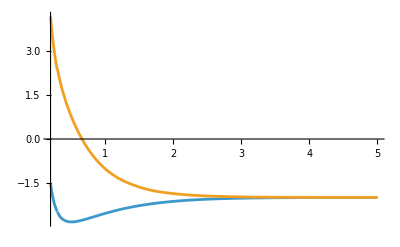

```mathematica
geradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
geradePotential=Table[{geradeData[[i,1]],geradeData[[i,3]]},{i,1,27}];
ungeradeData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];
ungeradePotential=Table[{ungeradeData[[i,1]],ungeradeData[[i,3]]},{i,1,27}];
long[R_]:=-2.0-0.082/R^4;
geradefun=Interpolation[geradePotential];
ungeradefun=Interpolation[ungeradePotential];
(* Fit to a model *)
gdata=Drop[geradePotential,{5,27}];
udata=Drop[ungeradePotential,{5,27}];
model[R_,C1_,C2_,C3_]:=C1 Exp[-C2 R]/R+C3;
gnlm=NonlinearModelFit[gdata,model[R,C1,C2,C3],{C1,C2,C3},R];
unlm=NonlinearModelFit[udata,model[R,C1,C2,C3],{C1,C2,C3},R];
gshort[R_]:=model[R,C1,C2,C3] /. gnlm["BestFitParameters"];
ushort[R_]:=model[R,C1,C2,C3] /. unlm["BestFitParameters"];
gpot[R_]=Piecewise[{{gshort[R],R<=0.3},{geradefun[R],0.3<R<13.0},{long[R],R>=13.0}}];
upot[R_]=Piecewise[{{ushort[R],R<=0.3},{ungeradefun[R],0.3<R<13.0},{long[R],R>=13.0}}];
Plot[{gpot[R],upot[R]},{R,0.2,5},PlotRange->All]

(*e=0.1/27.21;*)
μ=1866.0/2.0;
(*k=√(2 μ e);*)
kB = 8.617^-5;  (* Boltzman, eV/K *)
(*λ=2π/k*)

r0=0.01;
rend=100;

computePhaseShifts[m_,e_,r0_,rend_]:=Module[{k,eqG,eqU,solsG,solsU,fg,fu},
k=√(2 μ e);
equG:=yg''[r]+yg'[r]/r-2 μ  (gpot[r]+2)yg[r]-m^2/r^2 yg[r]+2 μ e yg[r] ;
equU:=yu''[r]+yu'[r]/r-2 μ  (upot[r]+2)yu[r]-m^2/r^2 yu[r]+2 μ e yu[r]; 
solsG=Flatten[NDSolve[{equG==0,yg[r0]==0,yg'[r0]==1},yg,{r,r0,rend},MaxSteps->200000]];
solsU=Flatten[NDSolve[{equU==0,yu[r0]==0,yu'[r0]==1},yu,{r,r0,rend},MaxSteps->200000]];
fg[r_]=yg[r] /. solsG;
fu[r_]=yu[r] /. solsU;
(*Print[Plot[fg[r],{r,r0,rend}]];
Print[Plot[fu[r],{r,r0,rend}]];*)
(*Print[Plot[fg[r]-fu[r],{r,r0,rend}]]*)
ylogG[r_]:=fg'[r]/fg[r];
ylogU[r_]:=fu'[r]/fu[r];
(*Print[Plot[ylogG[r],{r,r0,rend}]];
Print[Plot[ylogU[r],{r,r0,rend}]];*)
sl[n_,r_]:=BesselJ[n,k r];
cl[n_,r_]:= HankelH1[n, k r];
slp[n_,r_]:=Derivative[0,1][sl][n,r];
clp[n_,r_]:=Derivative[0,1][cl][n,r];
bG[n_,r_]:=(-I)^(Abs[n])( slp[n,r]-ylogG[r] sl[n,r])/( clp[n,r]-ylogG[r]cl[n,r]);
bU[n_,r_]:=(-I)^(Abs[n])( slp[n,r]-ylogU[r] sl[n,r])/( clp[n,r]-ylogU[r]cl[n,r]);
(N[Abs[bG[m,rend]-bU[m,rend]]])^2
(*Sin[N[Abs[bG[m,rend]-bU[m,rend]]]]^2*)
];
(*computePhaseShifts[10,0.003,0.1,100]*)
```

```mathematica
(* e = collision energy in eV, r0, rend - R range *)
computeCrossSect[eV_,r0_,rend_]:= Module[{allBs,eH,k,crossSection},
eH = eV/27.21;  (* energy Hartree *)
k=√(2 μ eH);
Print["e=",eV, ", ", eH];
(* m - partial waves *)allBs = Table[{m,computePhaseShifts[m,eH,r0,rend]},{m,0,40}];
crossSection=1/k Total[allBs,{1}][[2]];
{eV,crossSection}
];

crossSection = Table[computeCrossSect[e, r0, rend],{e, 0.001,0.01, 0.001}];
crossSection // TableForm

crossSectionGraph = Interpolation[crossSection];
```

e=0.001, 0.0000367512

e=0.002, 0.0000735024

e=0.003, 0.000110254

e=0.004, 0.000147005

e=0.005, 0.000183756

e=0.006, 0.000220507

e=0.007, 0.000257258

e=0.008, 0.00029401

e=0.009, 0.000330761

e=0.01, 0.000367512

t | 6.99973
t | 7.70778
t | 6.95069
t | 6.00956
t | 5.62727
t | 5.31321
t | 5.08442
t | 4.93116
t | 4.8036
t | 4.63768

Interpolation::indat: Data point {t,6.99973} contains abscissa t, which is not a real number.

```mathematica
Plot[crossSectionGraph[t],{t,100,200}, AxesOrigin->{0,0}]
```

Interpolation::inddp: The point 100.002 in dimension 1 is duplicated.

Interpolation::inddp: The point 102.043 in dimension 1 is duplicated.

-Graphics-

Note the convergence of b_(m=40) as a function of R; b_(40) is already small, you need to calculate all b_{m} m<40, before total cross section sum over partial waves converges

The above code demonstrates the convergence of b_{m} (related to a phase shift) defined by Eq. (23) in my notes. This code is for the gerade potentials, do the same for the ungerade potentials, calculated in Vpots.nb. Use Eq. (38) in my notes to determine CRT cross sections.

You need to calculate b_{m} for many partial waves m, before σ  converges for large m (note above m=40, almost converged as |b_{40}|^2 <<1. You may want to re-write this code in python, to speed it up.

When complete, make a plot of the total cross sections, as a function of collision energy.
In order to educate the reader you may want to include additional figures, such as the dependence
of the partial wave cross sections, or plot of the wave function as shown above. Your thesis should be comprehensive and offer a narrative to help the, non-specialist reader, understand what and why you are doing.